```mathematica
R0=6356.766`30;
ZtoH[Z_]=(Z R0)/(Z+R0);
HtoZ[H_]=(H R0)/(R0-H);
```

```mathematica
Hb={0,11,20,32,47,51,71,ZtoH[86]};
Zb = {0,HtoZ[Hb[[2]]],HtoZ[Hb[[3]]],HtoZ[Hb[[4]]],HtoZ[Hb[[5]]],HtoZ[Hb[[6]]],HtoZ[Hb[[7]]],86,91,110,120,1000};
Lb={-6.5`30,0,1,2.8`30,0,-2.8`30,-2,0,0,12,0,0};
Zcorr=Table[z,{z,80,86,1/2}];
Mcorr={1,0.999996`30,0.999989`30,0.999971`30,0.999941`30,0.999909`30,0.999870`30,0.999829`30,0.999786`30,0.999741`30,0.999694`30,0.999641`30,0.9995788`30};
Tinf=1000;
```

```mathematica
Tb={288.15`30,0,0,0,0,0,0,0,0,0,0,0};
b=2;
Tb[[b]]=Tb[[b-1]]+Lb[[b-1]](Hb[[b]]-Hb[[b-1]]);
b=3;
Tb[[b]]=Tb[[b-1]]+Lb[[b-1]](Hb[[b]]-Hb[[b-1]]);
b=4;
Tb[[b]]=Tb[[b-1]]+Lb[[b-1]](Hb[[b]]-Hb[[b-1]]);
b=5;
Tb[[b]]=Tb[[b-1]]+Lb[[b-1]](Hb[[b]]-Hb[[b-1]]);
b=6;
Tb[[b]]=Tb[[b-1]]+Lb[[b-1]](Hb[[b]]-Hb[[b-1]]);
b=7;
Tb[[b]]=Tb[[b-1]]+Lb[[b-1]](Hb[[b]]-Hb[[b-1]]);
b=8;
Tb[[b]]=(Tb[[b-1]]+Lb[[b-1]](Hb[[b]]-Hb[[b-1]]))Mcorr[[-1]];
b=9;
Tb[[b]]=Tb[[b-1]]+Lb[[b-1]](Zb[[b]]-Zb[[b-1]]);
b=10;
Tb[[b]]=240;
b=11;
Tb[[b]]=Tb[[b-1]]+Lb[[b-1]](Zb[[b]]-Zb[[b-1]]);
b=12;
Tb[[b]]=Tinf;
Tb//TableForm
```

288.15
216.65
216.65
228.65
270.65
270.65
214.65
186.86716669360826079978692382
186.86716669360826079978692382
240
360
1000

```mathematica
Tc=(Lb[[10]](Zb[[10]]-Zb[[9]])Tb[[10]]+Tb[[9]]^2-Tb[[10]]^2)/(Lb[[10]](Zb[[10]]-Zb[[9]])+2Tb[[9]]-2Tb[[10]])
bigA=Tb[[9]]-Tc
littleA=((Zb[[10]]-Zb[[9]])bigA)/(√(bigA^2-(Tb[[10]]-Tc)^2))
λ=N[Lb[[10]]/(Tinf-Tb[[11]])]
```

263.1906471790912887537992211

-76.3234804854830279540122973

-19.9428815545855327095184745

0.01875

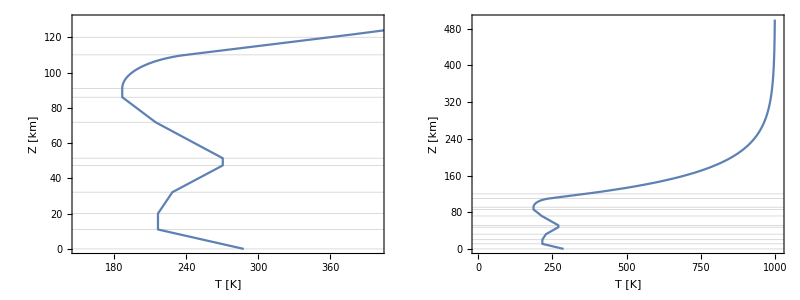

```mathematica
T[Z_]=Piecewise[{
{Tb[[1]]+Lb[[1]](ZtoH[Z]-Hb[[1]]),Zb[[1]]≤Z<Zb[[2]]},
{Tb[[2]],Zb[[2]]≤Z≤Zb[[3]]},
{Tb[[3]]+Lb[[3]](ZtoH[Z]-Hb[[3]]),Zb[[3]]<Z≤Zb[[4]]},
{Tb[[4]]+Lb[[4]](ZtoH[Z]-Hb[[4]]),Zb[[4]]<Z<Zb[[5]]},
{Tb[[5]],Zb[[5]]≤Z≤Zb[[6]]},
{Tb[[6]]+Lb[[6]](ZtoH[Z]-Hb[[6]]),Zb[[6]]<Z≤Zb[[7]]},
{Piecewise[{
{Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]),Zb[[7]]<Z≤Zcorr[[1]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[1]]+((Mcorr[[2]]-Mcorr[[1]])(Z-Zcorr[[1]]))/(Zcorr[[2]]-Zcorr[[1]])),Zcorr[[1]]<Z≤Zcorr[[2]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[2]]+((Mcorr[[3]]-Mcorr[[2]])(Z-Zcorr[[2]]))/(Zcorr[[3]]-Zcorr[[2]])),Zcorr[[2]]<Z≤Zcorr[[3]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[3]]+((Mcorr[[4]]-Mcorr[[3]])(Z-Zcorr[[3]]))/(Zcorr[[4]]-Zcorr[[3]])),Zcorr[[3]]<Z≤Zcorr[[4]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[4]]+((Mcorr[[5]]-Mcorr[[4]])(Z-Zcorr[[4]]))/(Zcorr[[5]]-Zcorr[[4]])),Zcorr[[4]]<Z≤Zcorr[[5]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[5]]+((Mcorr[[6]]-Mcorr[[5]])(Z-Zcorr[[5]]))/(Zcorr[[6]]-Zcorr[[5]])),Zcorr[[5]]<Z≤Zcorr[[6]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[6]]+((Mcorr[[7]]-Mcorr[[6]])(Z-Zcorr[[6]]))/(Zcorr[[7]]-Zcorr[[6]])),Zcorr[[6]]<Z≤Zcorr[[7]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[7]]+((Mcorr[[8]]-Mcorr[[7]])(Z-Zcorr[[7]]))/(Zcorr[[8]]-Zcorr[[7]])),Zcorr[[7]]<Z≤Zcorr[[8]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[8]]+((Mcorr[[9]]-Mcorr[[8]])(Z-Zcorr[[8]]))/(Zcorr[[9]]-Zcorr[[8]])),Zcorr[[8]]<Z≤Zcorr[[9]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[9]]+((Mcorr[[10]]-Mcorr[[9]])(Z-Zcorr[[9]]))/(Zcorr[[10]]-Zcorr[[9]])),Zcorr[[9]]<Z≤Zcorr[[10]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[10]]+((Mcorr[[11]]-Mcorr[[10]])(Z-Zcorr[[10]]))/(Zcorr[[11]]-Zcorr[[10]])),Zcorr[[10]]<Z≤Zcorr[[11]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[11]]+((Mcorr[[12]]-Mcorr[[11]])(Z-Zcorr[[11]]))/(Zcorr[[12]]-Zcorr[[11]])),Zcorr[[11]]<Z≤Zcorr[[12]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[12]]+((Mcorr[[13]]-Mcorr[[12]])(Z-Zcorr[[12]]))/(Zcorr[[13]]-Zcorr[[12]])),Zcorr[[12]]<Z≤Zcorr[[13]]}
}],Zb[[7]]<Z≤Zb[[8]]},
{Tb[[8]],Zb[[8]]<Z≤Zb[[9]]},
{Tc+bigA √(1-((Z-Zb[[9]])/littleA)^2),Zb[[9]]<Z≤Zb[[10]]},
{Tb[[10]]+Lb[[10]](Z-Zb[[10]]),Zb[[10]]<Z≤Zb[[11]]},
{Tinf-(Tinf-Tb[[11]])ⅇ^(-(Lb[[10]]/(Tinf-Tb[[11]]))(((Z-Zb[[11]])(R0+Zb[[11]]))/(R0+Z))),Zb[[11]]<Z≤Zb[[12]]}
}];
Grid[{{
ParametricPlot[{T[Z],Z},{Z,0,130},PlotRange->{{150,400},{0,130}},AspectRatio->1.5,ImageSize->Medium,Exclusions->None,Frame->True,FrameLabel->{"T [K]","Z [km]"},GridLines->{None,Partition[Riffle[Zb,{{Dashed,Thin}}],2]}],
ParametricPlot[{T[Z],Z},{Z,0,500},PlotRange->{{0,1010},{0,500}},AspectRatio->1.5,ImageSize->Medium,Exclusions->None,Frame->True,FrameLabel->{"T [K]","Z [km]"},GridLines->{None,Partition[Riffle[Zb,{{Dashed,Thin}}],2]}]
}}]
```

```mathematica
Pb={101325,0,0,0,0,0,0,0};
g0=9.80665`30;
M0=28.964425912034`30;
R=8.31432`30;
Na=6.022169`30 10^26;
b=2;
Pb[[b]]=Pb[[b-1]](Tb[[b-1]]/Tb[[b]])^((g0 M0)/(R Lb[[b-1]]));
b=3;
Pb[[b]]=Pb[[b-1]] ⅇ^(-(g0 M0(Hb[[b]]-Hb[[b-1]]))/(R Tb[[b-1]]));
b=4;
Pb[[b]]=Pb[[b-1]](Tb[[b-1]]/Tb[[b]])^((g0 M0)/(R Lb[[b-1]]));
b=5;
Pb[[b]]=Pb[[b-1]](Tb[[b-1]]/Tb[[b]])^((g0 M0)/(R Lb[[b-1]]));
b=6;
Pb[[b]]=Pb[[b-1]] ⅇ^(-(g0 M0 (Hb[[b]]-Hb[[b-1]]))/(R Tb[[b-1]]));
b=7;
Pb[[b]]=Pb[[b-1]](Tb[[b-1]]/Tb[[b]])^((g0 M0)/(R Lb[[b-1]]));
b=8;
Pb[[b]]=Pb[[b-1]](Tb[[b-1]]/Tb[[b]])^((g0 M0)/(R Lb[[b-1]]));Pb//TableForm
```

101325
22632.03362389728402750167814
5474.874376757307085858952942
868.014988510785148131379345
110.90562914370221282848871
66.9384346263881217464974074
3.95638449983647254755145701
0.370699003145549604158616946

```mathematica
n7={1.129794`30 10^20,8.6`30 10^16,3.030898`30 10^19,1.351400`30 10^18,7.5817`30 10^14};
Mi={28.0134`30,15.9994`30,31.9988`30,39.948`30,4.0026`30,1.00794`30};
g[Z_]=g0(R0/(R0+Z))^2;
dTdZ[Z_]=D[T[Z],Z];
K7=1.2`30 10^2;
K[Z_]=Piecewise[{{K7,Z<95},{K7 ⅇ^(1-400/(400-(Z-95)^2)),95≤Z<115},{0,Z≥115}}];
a={0,6.986`30 10^20,4.863`30 10^20,4.487`30 10^20,1.700`30 10^21,3.305`30 10^21};
b={0,0.750`30,0.750`30,0.870`30,0.691`30,0.500`30};
α={0,0,0,0,-0.40`30,-0.25`30};
Q={0,-5.809644`30 10^-4,1.366212`30 10^-4,9.434079`30 10^-5,-2.457369`30 10^-4};
U={0,56.90311`30,86,86,86};
W={0,2.706240`30 10^-5,8.333333`30 10^-5,8.333333`30 10^-5,6.666667`30 10^-4};
q={0,-3.416248`30 10^-3,0,0,0};
u={0,97,0,0,0};
w={0,5.008765`30 10^-4,0,0,0};
```

```mathematica
nN2integrand[z_]=Piecewise[{{(M0 g[z])/(R T[z]),z≤100},{(Mi[[1]] g[z])/(R T[z]),z>100}}];
nN2int[Z_?NumericQ]:=NIntegrate[nN2integrand[z],{z,Zb[[8]],Z},PrecisionGoal->20,WorkingPrecision->50];
nN2[Z_]=n7[[1]] Tb[[8]]/T[Z] ⅇ^(-nN2int[Z]);
```

```mathematica
zBreaks={86,91,110,120,100};
Table[{zBreaks[[i]],NIntegrate[nN2integrand[z],{z,Zb[[8]],zBreaks[[i]]},PrecisionGoal->20,WorkingPrecision->50]},{i,1,Length[zBreaks]}]//TableForm
```

86 | 0.
91 | 0.88917387123689358224038646016166821067675823670132
110 | 3.9815997728018476144943716076509348722899852905653
120 | 5.0588195691573031407213147168888634469270696473818
100 | 2.4639390409132485651131706271460928722731372439656

```mathematica
D2[Z_?NumericQ]:=a[[2]]/nN2[Z](T[Z]/(273.15`30))^b[[2]]
nO1integrand[z_]=Piecewise[{
{g[z]/(R T[z])D2[z]/(D2[z]+K[z])(Mi[[2]]+(M0 K[z])/D2[z])+Q[[2]](z-U[[2]])^2 ⅇ^(-W[[2]](z-U[[2]])^3)+q[[2]](u[[2]]-z)^2 ⅇ^(-w[[2]](u[[2]]-z)^3),86≤z≤97},
{g[z]/(R T[z])D2[z]/(D2[z]+K[z])(Mi[[2]]+(M0 K[z])/D2[z])+Q[[2]](z-U[[2]])^2 ⅇ^(-W[[2]](z-U[[2]])^3),97<z≤100},
{g[z]/(R T[z])D2[z]/(D2[z]+K[z])(Mi[[2]]+(Mi[[1]] K[z])/D2[z])+Q[[2]](z-U[[2]])^2 ⅇ^(-W[[2]](z-U[[2]])^3),100<z<115},
{g[z]/(R T[z])Mi[[2]]+Q[[2]](z-U[[2]])^2 ⅇ^(-W[[2]](z-U[[2]])^3),z≥115}
}];
nO1int[Z_?NumericQ]:=NIntegrate[nO1integrand[z],{z,Zb[[8]],Z},PrecisionGoal->20,WorkingPrecision->50]
nO1[Z_]:=n7[[2]] Tb[[8]]/T[Z] ⅇ^(-nO1int[Z])
```

```mathematica
zBreaks={91,95,97,100,110,115,120};
Table[{zBreaks[[i]],NIntegrate[nO1integrand[z],{z,Zb[[8]],zBreaks[[i]]},PrecisionGoal->20,WorkingPrecision->50]},{i,1,Length[zBreaks]}]//TableForm
```

91 | -1.233515878553202473732870359381722709159578239846
95 | -1.6326227572400966458392137698551918713222318323254
97 | -1.673639650693629533581732048336911063344549458002
100 | -1.6519505201748717367834936553891625019117490443735
110 | -1.2350403922105527670969034237102425933231734729762
115 | -0.98014972401199733634679585609063050812531660217869
120 | -0.73123387388396381656282663442442532841310575735132

```mathematica
D3[Z_?NumericQ]:=a[[3]]/nN2[Z](T[Z]/(273.15`30))^b[[3]]
nO2integrand[z_]=Piecewise[{
{g[z]/(R T[z])D3[z]/(D3[z]+K[z])(Mi[[3]]+(M0 K[z])/D3[z])+Q[[3]](z-U[[3]])^2 ⅇ^(-W[[3]](z-U[[3]])^3),z≤100},
{g[z]/(R T[z])D3[z]/(D3[z]+K[z])(Mi[[3]]+(Mi[[1]] K[z])/D3[z])+Q[[3]](z-U[[3]])^2 ⅇ^(-W[[3]](z-U[[3]])^3),100<z<115},
{g[z]/(R T[z])Mi[[3]]+Q[[3]](z-U[[3]])^2 ⅇ^(-W[[3]](z-U[[3]])^3),z≥115}
}];
nO2int[Z_?NumericQ]:=NIntegrate[nO2integrand[z],{z,Zb[[8]],Z},PrecisionGoal->20,WorkingPrecision->50]
nO2[Z_]:=n7[[3]] Tb[[8]]/T[Z] ⅇ^(-nO2int[Z])
```

```mathematica
zBreaks={91,95,97,100,110,115,120};
Table[{zBreaks[[i]],NIntegrate[nO2integrand[z],{z,Zb[[8]],zBreaks[[i]]},PrecisionGoal->20,WorkingPrecision->50]},{i,1,Length[zBreaks]}]//TableForm
```

91 | 0.89870896603012713816579637038035959122316827582781
95 | 1.6401385731339726344797297296479318966950288648142
97 | 2.0206764985042181646977953931314167487746252684886
100 | 2.6026369578525224013706902729531267621953196871627
110 | 4.5003526937771803252418035707784420024940743853097
115 | 5.2767050379951361412122952471154509181701839053879
120 | 5.8804681169361678862157398274221461436938966825372

```mathematica
D4[Z_?NumericQ]:=a[[4]]/(nN2[Z]+nO1[Z]+nO2[Z])(T[Z]/(273.15`30))^b[[4]]
nArintegrand[z_]=Piecewise[{
{g[z]/(R T[z])D4[z]/(D4[z]+K[z])(Mi[[4]]+(M0 K[z])/D4[z])+Q[[4]](z-U[[4]])^2 ⅇ^(-W[[4]](z-U[[4]])^3),z≤100},
{g[z]/(R T[z])D4[z]/(D4[z]+K[z])(Mi[[4]]+((Mi[[1]]nN2[z]+Mi[[2]]nO1[z]+Mi[[3]]nO2[z])/(nN2[z]+nO1[z]+nO2[z]) K[z])/D4[z])+Q[[4]](z-U[[4]])^2 ⅇ^(-W[[4]](z-U[[4]])^3),100<z<115},
{g[z]/(R T[z])Mi[[4]]+Q[[4]](z-U[[4]])^2 ⅇ^(-W[[4]](z-U[[4]])^3),z≥115}
}];
nArint[Z_?NumericQ]:=NIntegrate[nArintegrand[z],{z,Zb[[8]],Z},PrecisionGoal->3]
nAr[Z_]:=n7[[4]] Tb[[8]]/T[Z] ⅇ^(-nArint[Z])
```

```mathematica
D5[Z_?NumericQ]:=a[[5]]/(nN2[Z]+nO1[Z]+nO2[Z])(T[Z]/(273.15`30))^b[[5]]
nHeintegrand[z_]=Piecewise[{
{g[z]/(R T[z])D5[z]/(D5[z]+K[z])(Mi[[5]]+(M0 K[z])/D5[z]+(α[[5]]R)/g[z] dTdZ[z])+Q[[5]](z-U[[5]])^2 ⅇ^(-W[[5]](z-U[[5]])^3),z≤100},
{g[z]/(R T[z])D5[z]/(D5[z]+K[z])(Mi[[5]]+((Mi[[1]]nN2[z]+Mi[[2]]nO1[z]+Mi[[3]]nO2[z])/(nN2[z]+nO1[z]+nO2[z]) K[z])/D5[z]+(α[[5]]R)/g[z] dTdZ[z])+Q[[5]](z-U[[5]])^2 ⅇ^(-W[[5]](z-U[[5]])^3),100<z<115},{g[z]/(R T[z])(Mi[[5]]+(α[[5]]R)/g[z] dTdZ[z])+Q[[5]](z-U[[5]])^2 ⅇ^(-W[[5]](z-U[[5]])^3),z≥115}
}];
nHeint[Z_?NumericQ]:=NIntegrate[nHeintegrand[z],{z,Zb[[8]],Z},PrecisionGoal->3]
nHe[Z_]:=n7[[5]] Tb[[8]]/T[Z] ⅇ^(-nHeint[Z])
```

```mathematica
nH11=8 10^10;
ϕ=7.2`30 10^11;
T11=T[500];
D6[Z_?NumericQ]:=a[[6]]/(nN2[Z]+nO1[Z]+nO2[Z]+nAr[Z]+nHe[Z])√(T[Z]/(273.15`30))
τ[Z_?NumericQ]:=NIntegrate[(g[z]Mi[[6]])/(R T[z]),{z,500,Z},PrecisionGoal->3]
nH[Z_]:=Piecewise[{
{0,Z<150},
{(nH11-NIntegrate[ϕ/D6[z](T[z]/T11)^(1+α[[6]])ⅇ^τ[z],{z,500,Z},PrecisionGoal->1])(T11/T[Z])^(1+α[[6]])ⅇ^(-τ[Z]),150≤Z<500},
{nH11,Z≥500}
}]
```

```mathematica
n[Z_]:=nN2[Z]+nO1[Z]+nO2[Z]+nAr[Z]+nHe[Z]+nH[Z]
```

```mathematica
j=0;
Zs=Table[Z,{Z,80,150,1/10}];
Ks=Table[{0,0},{Z,Zs}];
SetSharedVariable[j]
SetSharedVariable[Ks]
Monitor[
ParallelTable[Ks[[i]]={K[Zs[[i]]],Zs[[i]]};j=j+1,{i,1,Length[Zs],1},Method->"FinestGrained"],
ProgressIndicator[j/Length[Zs],ImageSize->{480,10}]
];
SetDirectory[NotebookDirectory[]];
DumpSave["Ks.mx",Ks];
```

```mathematica
j=0;
Zs=Table[Z,{Z,80,150,1/10}];
D2s=Table[{0,0},{Z,Zs}];
SetSharedVariable[j]
SetSharedVariable[D2s]
Monitor[
ParallelTable[D2s[[i]]={D2[Zs[[i]]],Zs[[i]]};j=j+1,{i,1,Length[Zs],1},Method->"FinestGrained"],
ProgressIndicator[j/Length[D2s],ImageSize->{480,10}]
];
SetDirectory[NotebookDirectory[]];
DumpSave["D2s.mx",D2s];
```

```mathematica
j=0;
Zs=Table[Z,{Z,80,150,1/10}];
D3s=Table[{0,0},{Z,Zs}];
SetSharedVariable[j]
SetSharedVariable[D3s]
Monitor[
ParallelTable[D3s[[i]]={D3[Zs[[i]]],Zs[[i]]};j=j+1,{i,1,Length[Zs],1},Method->"FinestGrained"],
ProgressIndicator[j/Length[D3s],ImageSize->{480,10}]
];
SetDirectory[NotebookDirectory[]];
DumpSave["D3s.mx",D3s];
```

```mathematica
j=0;
Zs=Table[Z,{Z,80,150,1/10}];
D4s=Table[{0,0},{Z,Zs}];
SetSharedVariable[j]
SetSharedVariable[D4s]
Monitor[
ParallelTable[D4s[[i]]={D4[Zs[[i]]],Zs[[i]]};j=j+1,{i,1,Length[Zs],1},Method->"FinestGrained"],
ProgressIndicator[j/Length[D4s],ImageSize->{480,10}]
];
SetDirectory[NotebookDirectory[]];
DumpSave["D4s.mx",D4s];
```

```mathematica
j=0;
Zs=Table[Z,{Z,80,150,1/10}];
D5s=Table[{0,0},{Z,Zs}];
SetSharedVariable[j]
SetSharedVariable[D5s]
Monitor[
ParallelTable[D5s[[i]]={D5[Zs[[i]]],Zs[[i]]};j=j+1,{i,1,Length[Zs],1},Method->"FinestGrained"],
ProgressIndicator[j/Length[D5s],ImageSize->{480,10}]
];
SetDirectory[NotebookDirectory[]];
DumpSave["D5s.mx",D5s];
```

```mathematica
j=0;
Zs=Table[Z,{Z,145,150,1/10}];
D6s=Table[{0,0},{Z,Zs}];
SetSharedVariable[j]
SetSharedVariable[D6s]
Monitor[
ParallelTable[D6s[[i]]={D6[Zs[[i]]],Zs[[i]]};j=j+1,{i,1,Length[Zs],1},Method->"FinestGrained"],
ProgressIndicator[j/Length[D6s],ImageSize->{480,10}]
];
SetDirectory[NotebookDirectory[]];
DumpSave["D6s.mx",D6s];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Ks.mx"
<<"D2s.mx"
<<"D3s.mx"
<<"D4s.mx"
<<"D5s.mx"
<<"D6s.mx"
```

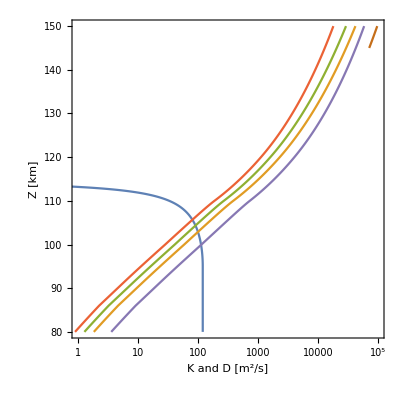

```mathematica
ListLogLinearPlot[{Ks,D2s,D3s,D4s,D5s,D6s},Joined->True,PlotRange->{{10^0,10^5},{80,150}},AspectRatio->1,AxesOrigin->{1,80},Frame->True,FrameLabel->{"K and D [m^2/s]","Z [km]"},GridLines->Automatic]
```

```mathematica
nN2s=ParallelTable[{nN2[Z],Z},{Z,86,1000,5}];
SetDirectory[NotebookDirectory[]];
DumpSave["nN2s.mx",nN2s];
```

```mathematica
nO1s=ParallelTable[{nO1[Z],Z},{Z,86,1000,5}];
```

```mathematica
nO2s=ParallelTable[{nO2[Z],Z},{Z,86,1000,5}];
SetDirectory[NotebookDirectory[]];
DumpSave["nO2s.mx",nO2s];
```

```mathematica
nArs=ParallelTable[{nAr[Z],Z},{Z,86,1000,5}];
SetDirectory[NotebookDirectory[]];
DumpSave["nArs.mx",nArs];
```

```mathematica
nHes=ParallelTable[{nHe[Z],Z},{Z,86,1000,5}];
SetDirectory[NotebookDirectory[]];
DumpSave["nHes.mx",nHes];
```

```mathematica
nHs=ParallelTable[{nH[Z],Z},{Z,86,1000,5},Method->"FinestGrained"];
SetDirectory[NotebookDirectory[]];
DumpSave["nHs.mx",nHs];
```

```mathematica
nTot=Partition[Riffle[nN2s[[;;,1]]+nO1s[[;;,1]]+nO2s[[;;,1]]+nArs[[;;,1]]+nHes[[;;,1]]+nHs[[;;,1]],nN2s[[;;,2]]],2];
SetDirectory[NotebookDirectory[]];
DumpSave["nTot.mx",nTot];
```

```mathematica
nO1s=Join[ParallelTable[{nO1[Z],Z},{Z,86,125,1}],ParallelTable[{nO1[Z],Z},{Z,126,1000,5}]];
SetDirectory[NotebookDirectory[]];
DumpSave["nO1s.mx",nO1s];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"nN2s.mx"
```

DumpGet::bgabi: File /home/pi/Downloads/USSA76/nN2s.mx was written with ABI 64, which is not compatible with this version of the Wolfram Language.

$Failed

```mathematica
SetDirectory[NotebookDirectory[]];
<<"nO1s.mx"
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"nO2s.mx"
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"nArs.mx"
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"nHes.mx"
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"nHs.mx"
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"nTot.mx"
```

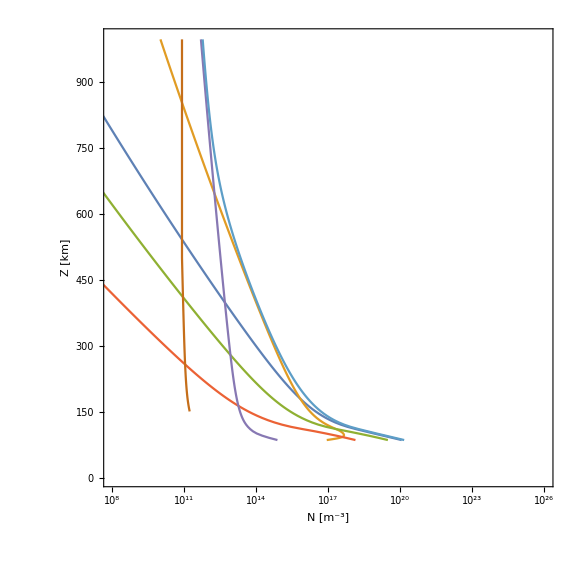

```mathematica
ListLogLinearPlot[{nN2s,nO1s,nO2s,nArs,nHes,nHs,nTot},Joined->True,PlotRange->{{10^8,10^26},{0,1000}},ImageSize->Large,AspectRatio->1,AxesOrigin->{8,0},Frame->True,FrameLabel->{"N [m^-3]","Z [km]"},GridLines->All]
```

```mathematica
zTest={86,90,91,92,97,100,110,120,250,500};
Table[{zTest[[i]],1/Na(Mi[[1]]nN2[zTest[[i]]]+Mi[[2]]nO1[zTest[[i]]]+Mi[[3]]nO2[zTest[[i]]])},{i,1,Length[zTest]}]//TableForm
```

86 | 6.868229804882592966089128352×10^-6
90 | 3.372692865868099617239024033×10^-6
91 | 2.823433219432365715969566504×10^-6
92 | 2.362332169742465636928814161×10^-6
97 | 9.569414013440917575136807884×10^-7
100 | 5.54100150967292213883613239×10^-7
110 | 9.63811722191249588316869198×10^-8
120 | 2.2130339311319628356887724854×10^-8
250 | 6.0650345521495019572901501937×10^-11
500 | 5.0001262238200813767204179509×10^-13

```mathematica
zTest={86,90,91,92,97,100,115,250};
Table[{zTest[[i]],nN2[zTest[[i]]],nO1[zTest[[i]]],nO2[zTest[[i]]]},{i,1,Length[zTest]}]//TableForm
```

86 | 1.129794×10^20 | 8.6×10^16 | 3.030898×10^19
90 | 5.546521479267254794971999057×10^19 | 2.443463760311834144127988965×10^17 | 1.479474226700614678455534251×10^19
91 | 4.64339851622632161604012005×10^19 | 2.952620227448374691572625856×10^17 | 1.233863099904780519724661979×10^19
92 | 3.885664319226942149172991342×10^19 | 3.43430592241452108091855385×10^17 | 1.02702283902131752863596259×10^19
97 | 1.581048236783453854368408287×10^19 | 4.499967185978831562919649341×10^17 | 3.943311622200324315756315897×10^18
100 | 9.20961742392874479774765678×10^18 | 4.29782671726576376189935704×10^17 | 2.15069045037773394154434104×10^18
115 | 7.2540233700801279948658540733×10^17 | 1.4275252997795138566311663026×10^17 | 9.6458207388702323943490227358×10^16
250 | 4.825472888586457326039153612×10^14 | 1.3883359060966573873726876398×10^15 | 2.482378545970372274507060571×10^13